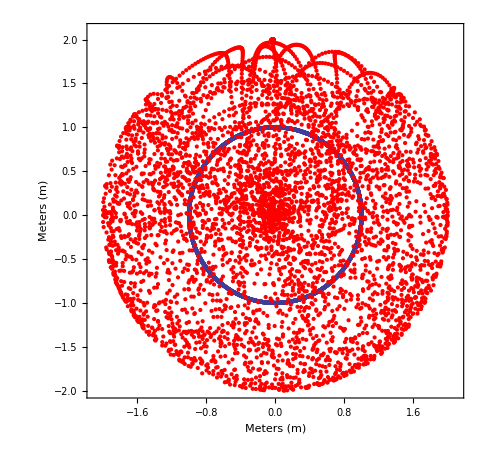

```mathematica
m1 =Import["/home/dk0r/git/comp-phys/Final_Project/M1_position.csv"];
m2 =Import["/home/dk0r/git/comp-phys/Final_Project/M2_position.csv"];

pm1 = ListPlot[m1];
pm2 = ListPlot[m2,PlotStyle->Red];

Show[pm1,pm2, PlotRange->{{-2.1,2.1},{-2,2.1}},AspectRatio->Automatic, LabelStyle->{FontSize->15},Frame->True,FrameLabel->{"Meters (m)","Meters (m)"}]
```